```mathematica
wacc[f_,T_,σ_]:=f-Log[1-Erf[σ*2^(-3/2)]]/T
```

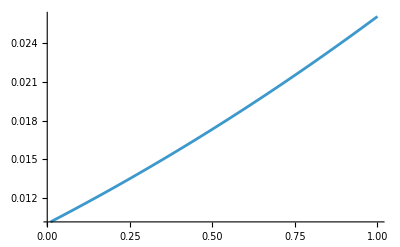

```mathematica
Plot[wacc[0.01,30,σ],{σ,0.01,1.0}]
```